To do: be more quantitative and check that J evolves at the correct rate according to the paper
Don’t define variables so early, do it like the noise code
Change the way pulses are defined like the noise code
Plot contrast as a function of time

### Parameters

```mathematica
Ω=1000 π;δω0=5{-1,1}π;tRes=0.001;J=2π;tMax=5;ψ0=ge;pulseList=xy8Core;θ=.;
parameters=StringForm["Ω=``,δω0=``,J=``,tMax=``,τ0=``,ψ0=``",Ω,δω0,J,tMax,τ0,ψ0];
```

### Load

#### Options

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->True];
```

#### States

```mathematica
qubits=2;g={{1},{0}};e={{0},{1}};gg=KroneckerProduct[g,g];ge=KroneckerProduct[g,e];{Φp,Φm}=(#@@{KroneckerProduct[g,g],KroneckerProduct[e,e]})/(√2)&/@{Plus,Subtract};{Ψp,Ψm}=(#@@{KroneckerProduct[g,e],KroneckerProduct[e,g]})/(√2)&/@{Plus,Subtract};
```

#### Pulses

```mathematica
xN[n_]:=Join[{{π/2,"x",0},{π,"x",τ}},Table[{π,"x",2 τ},n],{{π/2,"x",τ}}]
```

```mathematica
xy8Core={{π,"x",2τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"x",2 τ}};
xy8NCore={};Do[AppendTo[xy8NCore,xy8Core],10];xy8NCore=Flatten[xy8NCore,1];xy8NCore[[1]]={π,"x",0};
xy8N=Join[{{π/2,"x",0},{π,"x",τ}},xy8NCore[[2;;]],{{π/2,"x",τ}}];
```

```mathematica
free={{π,"y",0,1}};
ramsey={{π/2,"x",0},{π/2,"x",τ},{π/2,{Cos[θ],Sin[θ],0},τ}};
spinEcho={{π/2,"x",0},{π,"x",τ},{π/2,"x",τ}};
xy8={{π/2,"x",0},{π,"x",τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π/2,"x",τ}};
x8={{π/2,"x",0},{π,"x",τ},{π,"x",2 τ},{π,"x",2 τ},{π,"x",2 τ},{π,"x",2 τ},{π,"x",2 τ},{π,"x",2 τ},{π,"x",2 τ},{π/2,"x",τ}};
xy8Core={{π,"x",0},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"x",2 τ}};
```

#### Hamiltonians

```mathematica
σ={σx,σy,σz}=(PauliMatrix[#1]&)/@{1,2,3};σp=σx+ⅈ σy;σm=σx-ⅈ σy;
conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj;Hpulse[vec_]:=1/2 Ω ∑_(n=1)^3 σ⟦n⟧ Normalize[vec]⟦n⟧
H0Single[n_]:=1/2 δω0⟦n⟧ σz
HJ=J/8 (KroneckerProduct[σp,σm]+KroneckerProduct[σm,σp]);H0=KroneckerProduct[IdentityMatrix[2],H0Single[2]]+KroneckerProduct[H0Single[1],IdentityMatrix[2]]+HJ;idList=ConstantArray[IdentityMatrix[2],qubits];
H[vec_,numbers_]:=H0+Plus@@Table[KroneckerProduct@@ReplacePart[idList,i->Hpulse[vec]],{i,numbers}];
```

#### Unitary matrices

```mathematica
U[t_,t0_,tf_,vec_,number_]:=N[MatrixExp[-ⅈ H[vec,number] Piecewise[{{t-t0,t0<t<tf},{tf-t0,t≥tf}}]]];createUnitary[t_,pulseList_,τ0_]:=Module[{tStarts,tEnds,vecs,pulseStates,tsI},vecs=pulseList⟦All,2⟧/.{"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}};vecs=Flatten[MapThread[{#1,#2}&,{vecs,ConstantArray[0,pulses]}],1];vecs=vecs⟦1;;-1-(pulses-gaps)⟧;pulseStates=ConstantArray[1,pulses];Do[If[Length[pulseList⟦n⟧]==4,pulseStates⟦n⟧=pulseList⟦n,4⟧,pulseStates⟦n⟧=Range[1,qubits]],{n,1,pulses}];pulseStates=Flatten[MapThread[{#1,#2}&,{pulseStates,ConstantArray[0,pulses]}],1];pulseStates=pulseStates⟦1;;-1-(pulses-gaps)⟧;
tsI=tsF/.τ->τ0;Dot@@Reverse[MapThread[Hold[U],{ConstantArray[t,timeSteps-1],tsI⟦1;;-2⟧,tsI⟦2;;All⟧,vecs,pulseStates}]]]
```

#### Bloch sphere

```mathematica
createBlochVector[stateEvolution_]:=Module[{ux1,uy1,ux2,uy2,P1,P2},{ux1,uy1}=(N[ParallelTable[ComplexExpand[#1[(stateEvolution⟦n,1,1⟧+stateEvolution⟦n,2,1⟧)/(stateEvolution⟦n,3,1⟧+stateEvolution⟦n,4,1⟧+ⅈ/10^5)]],{n,1,1+tMax/tRes}]]&)/@{Re,Im};{ux2,uy2}=(N[ParallelTable[ComplexExpand[#1[(stateEvolution⟦n,1,1⟧+stateEvolution⟦n,3,1⟧)/(stateEvolution⟦n,2,1⟧+stateEvolution⟦n,4,1⟧+ⅈ/10^5)]],{n,1,1+tMax/tRes}]]&)/@{Re,Im};P1=ParallelTable[{(2 ux1⟦n⟧)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2),(2 uy1⟦n⟧)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2),(1-ux1⟦n⟧^2-uy1⟦n⟧^2)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2)},{n,1,1+tMax/tRes}];P2=ParallelTable[{(2 ux2⟦n⟧)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2),(2 uy2⟦n⟧)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2),(1-ux2⟦n⟧^2-uy2⟦n⟧^2)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2)},{n,1,1+tMax/tRes}];P1=(Interpolation[P1⟦All,#1⟧]&)/@{1,2,3};P2=(Interpolation[P2⟦All,#1⟧]&)/@{1,2,3};{P1,P2}]
blochSphere=Show[ParametricPlot3D[{Cos[θ],Sin[θ],0},{θ,0,2 π},PlotStyle->{Black,Dotted}],ParametricPlot3D[{0,Cos[θ],Sin[θ]},{θ,0,2 π},PlotStyle->{Black,Dotted}],ParametricPlot3D[{Sin[θ],0,Cos[θ]},{θ,0,2 π},PlotStyle->{Black,Dotted}],Graphics3D[{Text["x",{1.1,0,0}],Text["y",{0,1.1,0}],Text["z",{0,0,1.1}],{Arrow[{{-1,0,0},{1,0,0}}],Arrow[{{0,-1,0},{0,1,0}}],Arrow[{{0,0,-1},{0,0,1}}]},Opacity[0.3],Sphere[{0,0,0}]}]];
```

#### Plots

Creates a graphic of the pulse train.

```mathematica
plotPulses[pulseList_,τ1_]:=Quiet[Module[{tsPulse,recs,jPeriod,δωPeriod},tsPulse=Accumulate[Flatten[Thread[{pulseList⟦All,3⟧,pulseList⟦All,1⟧/Ω}]]];recs=Table[{EdgeForm[Directive[Thick,Which[SameQ[pulseList[[(n+1)/2,2]],"x"],Red,SameQ[pulseList[[(n+1)/2,2]],"y"],Blue,Not[SameQ[pulseList[[(n+1)/2,2]],"y"]],Darker[Green]]]],Rectangle[{tsPulse⟦n⟧/.τ->τ1,0},{tsPulse⟦n+1⟧/.τ->τ1,1}]},{n,1,Length[tsPulse],2}];
jPeriod={Lighter[Gray],Rectangle[{0,-.5},{Min[(2π)/J/.ComplexInfinity->Infinity,tsPulse[[-1]]/.τ->τ1],-1}]};
δωPeriod={Gray,Rectangle[{0,-1},{Min[(2π)/Abs[δω0[[1]]]/.ComplexInfinity->Infinity,tsPulse[[-1]]/.τ->τ1],-1.5}]};Graphics[{recs,jPeriod,δωPeriod},Axes->True,Ticks->{Automatic,None},PlotRange->{{0,tsPulse[[-1]]/.τ->τ1},{-1.5,1}},ImageSize->Full,AspectRatio->1/20]]];
```

Varies τ and plots the population at tMax in the 2-qubit basis.

```mathematica
plotFinalPop:=ListPlot[(Transpose[{tsF[[-1]]/.τ->(Range[Max[(2π)/Ω,tRes],τ0,tRes]),finalPops⟦All,#1,1⟧}]&)/@{1,2,3,4},PlotRange->All,PlotLabel->StringForm["Population over τ for δω_0=``",δω0[[2]]],PlotLegends->{"gg","ge","eg","ee"},ImageSize->Large,Joined->True,Frame->True,FrameLabel->{"tMax","population"}];
```

Plots the population in the 2-qubit basis as a function of time.

```mathematica
plotPopEvolution:=ListPlot[(Transpose[{Range[0,tMax,tRes],pops⟦All,#1,1⟧}]&)/@{1,2,3,4},PlotRange->All,PlotLabel->"Population of each state in the 2-qubit basis over time",PlotLegends->{"gg","ge","eg","ee"},ImageSize->Large,Joined->True,Frame->True,FrameLabel->{"time","population"}];
```

Plots the population of the 1st qubit as a function of time.

```mathematica
plotSingleQubitEvolution:=ListPlot[(Transpose[{Range[0,tMax,tRes],pops⟦All,#1,1⟧+pops⟦All,#1+1,1⟧}]&)/@{1,3},PlotRange->All,PlotLabel->"Population of the 1st qubit over time",PlotLegends->{"g","e"},ImageSize->Large,PlotStyle->{Blue,Red},Joined->True,Frame->True,FrameLabel->{"time","population"}];
```

Plots the parity of the 2-qubit state as a function of time.

```mathematica
plotParity:=ListPlot[(Transpose[{Range[0,tMax,tRes],pops⟦All,1,1⟧+pops⟦All,4,1⟧-pops⟦All,2,1⟧-pops⟦All,3,1⟧}]),PlotRange->All,PlotLabel->"Population of each state in the 2-qubit basis over time",PlotLegends->{"gg","ge","eg","ee"},ImageSize->Large,Joined->True,Frame->True,FrameLabel->{"time","population"}];
```

Plots the evolution of each qubit on the Bloch sphere over time.

```mathematica
plotBlochSphere:=Manipulate[{Show[Graphics3D[{{Blue,Thick,Arrow[{{0,0,0},{Px1[1+t/tRes],Py1[1+t/tRes],Pz1[1+t/tRes]}}]}},Boxed->False,PlotLabel->"Bloch spheres for qubits 1 and 2",ImageSize->Medium],ParametricPlot3D[{Px1[n],Py1[n],Pz1[n]},{n,1,1+tMax/tRes}],blochSphere],Show[Graphics3D[{{Red,Thick,Arrow[{{0,0,0},{Px2[1+t/tRes],Py2[1+t/tRes],Pz2[1+t/tRes]}}]}},Boxed->False],ParametricPlot3D[{Px2[n],Py2[n],Pz2[n]},{n,1,1+tMax/tRes},PlotStyle->Red],blochSphere,ImageSize->Medium]},{t,0,tMax,tRes}];
```

Varies θ and plots the probability of the first qubit being in the excited state at tMax.

```mathematica
plotSingleParticlePhaseContrast:=Module[{pop,single,contrast,θrange},
θrange=Range[-π,π,π/100];
pop=Table[Abs[(ReleaseHold[precompute[tMax]/.θ->θp].ψ0)]^2,{θp,θrange}];
single=pop[[All,3,1]]+pop[[All,4,1]];
contrast=Max[single]-Min[single];
ListPlot[Transpose@{θrange,single},FrameTicks->{Automatic,{Range[-π,π,π/2],None}},PlotRange->{0,1},PlotLabel->StringForm["Single Particle Phase Contrast: ``",Round[contrast,0.01]],FrameLabel->{"θ","P_e"}]]
plotParityPhaseContrast:=Module[{pop,parity,θrange},
θrange=Range[-π,π,π/100];
pop=Table[Abs[(ReleaseHold[precompute[tMax]/.θ->θp].ψ0)]^2,{θp,θrange}];
parity=pop[[All,1,1]]+pop[[All,4,1]]-pop[[All,2,1]]-pop[[All,3,1]];
ListPlot[Transpose@{θrange,parity},FrameTicks->{Automatic,{Range[-π,π,π/2],None}},PlotRange->{-1,1}]]
```

### Calculate

#### Find time steps

```mathematica
tsF=Accumulate[Flatten[Thread[{pulseList⟦All,3⟧,pulseList⟦All,1⟧/Ω}]]];
τ0=If[!FreeQ[tsF⟦-1⟧,τ],N[τ/.Solve[tMax==tsF⟦-1⟧,τ]⟦1⟧],tMax];
ts=tsF/.τ->τ0;
If[ts⟦-1⟧≠tMax,ts=Append[ts,tMax]];
pulses=Length[pulseList];
timeSteps=Length[ts];
gaps=timeSteps-pulses-1;
```

#### Check createUnitary

```mathematica
(*createUnitary[t,pulseList,τ0]*)
```

#### Precompute unitarity matrices

```mathematica
Usteps={IdentityMatrix[4]};
Do[Usteps=Append[Usteps,ReleaseHold[Reverse[createUnitary[ts⟦n+1⟧,pulseList,τ0]]⟦n⟧].Usteps⟦-1⟧],{n,1,Length[ts]-1}]
```

```mathematica
precompute[t_]:=Module[{pos},pos=If[t==0,1,Position[ts,Max[Select[ts,#1<t&]]]⟦-1,1⟧];Reverse[createUnitary[t,pulseList,τ0]]⟦pos⟧.Usteps⟦pos⟧]
```

#### Calculate time evolution

```mathematica
state=ParallelTable[ReleaseHold[precompute[t]/.θ->0].ψ0,{t,0,tMax,tRes}];
pops=(N[Abs[#1]^2]&)/@state;
```

```mathematica
(*bell[x_,bState_]:=Chop[Abs[hc[bState].x]^2[[1,1]]]
ListPlot[bell[#1,Φm]&/@state,PlotRange->All]*)
```

```mathematica
finalState=ParallelTable[ReleaseHold[createUnitary@@{tsF[[-1]],pulseList,τ}/.τ->n].ψ0,{n,Max[(2π)/Ω,tRes],τ0,tRes}];
finalPops=(N[Abs[#1]^2]&)/@finalState;
```

### Results

```mathematica
(*{{Px1,Py1,Pz1},{Px2,Py2,Pz2}}=createBlochVector[state];*)
(*plotBlochSphere*)
```

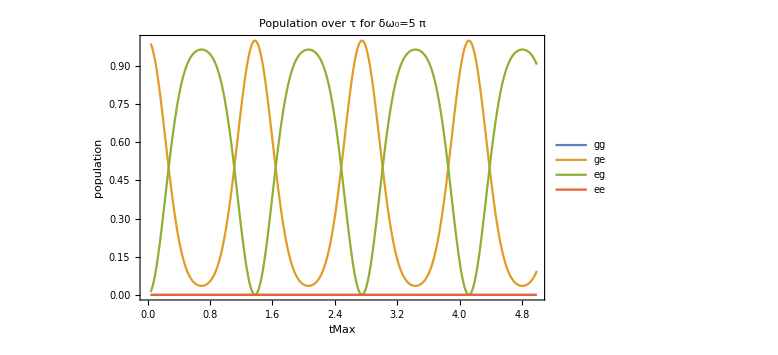

```mathematica
plotFinalPop
(*plotPulses[pulseList,τ0]*)
(*parameters
pulseList*)
(*plotPopEvolution*)
(*
plotSingleQubitEvolution
plotParity
plotSingleParticlePhaseContrast
plotParityPhaseContrast*)
```

```mathematica
parameters
```

Ω=1000 π,δω0={-7.85398,7.85398},J=π,tMax=5,τ0=0.356571,ψ0={{0},{1},{0},{0}}

Ω=1000 π,δω0={-5 π,5 π},J=2 π,tMax=5,τ0=0.356571,ψ0={{0},{1},{0},{0}}